```mathematica
Remove["Global`*"]
(*<<PhysicalConstants *)
<<Units`

(*<<VectorAnalysis`*)
<<FourierSeries`
(*<<LinearRegression`*)
```

```mathematica
(*Alpha in B11*)
AEtPR[x_]=-7886.280357710174-447433.3588072937/(-53.738273878096535-0.0021441505825878977 ⅇ^(-8.303724963590138 x))-439.42946638568924/x^0.00003948240578642675+1.6971767993392926 x+0.19024398671550105 x^2+0.06987417341402324 x^3-0.010988535270362 x^4+0.0008519646820542874 x^5-0.00002644158728776537 x^6;(*MeV to µm*)
APRtE=InverseFunction[AEtPR[#]&];

(*Proton in B11*)
EtPR[x_]=-4038.621695160617+30.217944902944236/(0.007481857100785539+3.2469601381813174*^-7 ⅇ^(-37.49736075902206 x))+3.307130653753605 x+1515.3152978046726 x^1.9990033267320544-1506.2506067955821 x^2+0.09463470541261623 x^3-0.13448967381673807 x^4+0.047932270219233936 x^5-0.005179352017528617 x^6;(*MeV to µm*)
PRtE= InverseFunction[EtPR[#]&];
(*1/(Stopping Power MeV/μm)*)
f[x_]=(4.419276392445275+ⅇ^(-7.3803552653244 (-0.10066107776724603+x))-0.5673657094346726/(1+0.7297860911389368 (-1.1106115256038274+x)^2)+0.5758738282552386/(1+1.030347643016361 (-0.9802921157540312+x)^3)+9.861753173526887 x-0.06433184715293583( x)^2+3.8810193819415244 Log[4.15270754026916 Abs[0.04038187709701176+x]]);

(* Cross Section Units: barns.  1 b = 10^-16 µm^2 *)
(*g[x_]=10^-16((.000002)/((x-.155)^2+.00005)+0.4*(Erf[(x-0.3)/(.06)]+1)*(.022)/((x-.63)^2+(0.3/2)^2)+(.012)/((x-1.4)^2+.1)+(.01)/((x-2.65)^2+.06)+0.03*(Erf[(x-1.2)/(.21)]+1));*)
g[x_]=10^-3*10^-16*(-3.5650236274749614+23.20200042365487/(0.045773195674098134+(-2.5808801675740694+x)^2)+4.287083868050379/(0.04657872865678219+(-1.4379138393368533+x)^2)+710883.2810500122/(-2.8453995938152443*^10+(7.167293360108095*^7+x)^2)-(36418.14230130918 (1+Erf[7.4769146951401755 (-0.7308497211376067+x)]))/(30.42724516180452+(-2.2968820148661604+x)^2)+1282.7470938628087 (1+Erf[4.493328010602532 (-0.5676324141957634+x)]));(*new cross section*)
(* Peak of Cross Section/Stopping Power*)
PeakPR=EtPR[0.6425599979725697];
(* Quantities of reaction *)
mp=1; (*mass of proton*)
mB11=11; (*mass of B11*)
mAlpha=4; (*mass of Be8*)(*This is M3 since this is the momentum of the particle your trying to calculate*)
mBe8=8; (*mass of Be8*)
QBe8=8.586; (*Q value of Be8*)
QBe8s= 5.65; (*Q value of excited Be8*)(*Excited is most common in reaction*)
Qa=.092; (*Q value for alpha_12 from non-excited Be8*)
Qas=3.028; (*Q value for alpha_12 from excited Be8*)
(*Ep=.66;*) 
p3[p1_,m3_,m4_,Etot_,θ_]:=1/(2 (1+m4/m3))(2 p1 Cos[π/180 θ]+√(4 p1^2 Cos[π/180 θ]^2-4(1+m4/m3)(p1^2-2 m4 Etot)));(*plus*)
p32[p1_,m3_,m4_,Etot_,θ_]:=1/(2 (1+m4/m3))(2 p1 Cos[π/180 θ]-√(4 p1^2 Cos[π/180 θ]^2-4(1+m4/m3)(p1^2-2 m4 Etot)));(*minus*)(*Determine momentum of 3rd particle in collision*)

γ[m1_,m2_,m3_,m4_,E1_,Q_]:=√((m1 m3)/(m2 m4) E1/(E1+Q(1+m1/m2))); 
θl[θc_,γ_]:=Which[θc==0,0,θc==180,180, ArcCot[(γ+Cos[θc Degree])/Sin[θc Degree]]/Degree<0,ArcCot[(γ+Cos[θc Degree])/Sin[θc Degree]]/Degree+180,ArcCot[(γ+Cos[θc Degree])/Sin[θc Degree]]/Degree>0,ArcCot[(γ+Cos[θc Degree])/Sin[θc Degree]]/Degree];(* between 0 or 180 *)
(* This will assist in relationship between L and C coordinates The Atomic Nucleus pg 421 *)
ECoeff=Join[{0.15,0.22,0.25,0.30,0.4,0.49,0.57,0.65,0.73,0.80,0.88,0.94,1.00,1.08},Array[1.2+(#*.1)&,27,0]]; (*Energies for Legendre polynomial fitting*)
CoeffG={{0.91,0.023,-0.011,0,0},{5.815,-0.272,-0.14,0,0},{9.307,0.019,-0.05,0,0},{20.837,-0.35,-0.73,0,0},{61.85,-0.03,0.46,0,0},{114.01,1.13,-1.27,0,0},{187.84,-1.19,3.44,0,0},{218.42,-3.17,6.31,0,0},{179.73,-3.86,8.84,0,0},{112.20,-5.40,8.07,0,0},{72.44,-3.11,6.76,0,0},{51.25,1.57,0.17,0,0},{48.78,2.01,0.28,0,0},{47.36,0.34,-0.15,0,0},{49.39,0.22,-3.60,0,0},{50.63,0.55,-5.34,0,0},{52.46,3.69,-3.79,1.84,1.03},{49.68,3.99,-3.87,1.86,0.10},{45.34,4.24,-3.31,2.04,0.91},{41.64,4.04,-2.64,2.06,1.05},{37.90,4.23,-1.49,2.38,1.31},{36.67,4.16,-0.93,2.57,1.67},{37.13,3.74,-0.95,1.23,1.95},{35.24,3.82,0.68,3.61,2.85},{39.78,3.51,1.94,5.49,4.29},{47.09,3.78,5.12,8.27,6.01},{58.98,3.61,13.06,11.32,7.55},{70.41,3.11,23.16,13.59,3.80},{82.63,3.53,30.33,10.77,-7.14},{71.20,3.58,16.39,3.74,-14.18},{51.92,3.70,0.94,2.15,-9.25},{41.91,3.85,-5.75,2.73,-2.02},{42.74,3.99,-4.45,5.49,5.29},{49.90,4.25,5.22,5.63,6.15},{55.69,4.90,7.37,5.72,3.27},{64.19,4.65,8.85,4.71,-0.37},{72.66,5.11,10.68,3.66,-3.64},{78.11,4.72,12.57,0.87,-3.79},{80.22,5.74,7.52,0.64,-9.46},{80.76,6.87,5.05,0.85,-10.46},{74.92,6.51,1.97,0.70,-9.13}}; (*Legendre polynomial fitting coefficients*)
Coeff[E_]:=CoeffG[[Position[ECoeff,Max[Nearest[ECoeff,E]]][[1,1]]]];(* Input incident energy for coresponding Legendre polynomial fitting coefficents *)
LegPolFit[E_,θ_]:=Total[Coeff[E]LegendreP[Range[0,4],Cos[θ Degree]]]; (* Input incident energy and angle.  Outputs fitted Legendre Coefficients *)
```

```mathematica
(* Angle and start *)
(*These angles are in center of mass frame Subscript[θ, C]*)
AngStt=30;
AngStp=160.;
AngBins=8;
AngStpsz=(AngStp-AngStt)/(AngBins-1);
Angles=Array[AngStt+(#-1)AngStpsz&,AngBins]
```

{30.,48.5714,67.1429,85.7143,104.286,122.857,141.429,160.}

```mathematica
(*step through different radiuses *)
radst=.001; (*start radius*)
radstp=45; (*stop radius*)
radBins=500; (*bins between start and stop*)
radStpSz=(radstp-radst)/(radBins-1); (* step size between start and stop *)
TIon=radii=Totala=Ent=Ext=Range[radBins];(*Tion = array of escaping ion energy of alpha, 
radii = array of radiuses program has simulated *)
```

```mathematica
For[ri=1,ri≤ radBins,ri++,
r=radst+(ri-1)radStpSz; (*r is the radius currenlty looking at*)
If[Mod[ri,10]==0,Print[ri]];
AVGThickCircle=1.5706375999552906;
(* 1/Stopping Power Units: µm/MeV.  1 µm = 10^-6 m.  1MeV = 1.6×10^-13 joules *)
AVGThick=r*AVGThickCircle;(*μm*)
PeakBins=50;
Start=If[PeakPR-AVGThick<0,0,PeakPR-AVGThick];
Stepsize=(PeakPR-Start)/(PeakBins-1);
IntN=Range[PeakBins];
(*Find the Energies to get max alphas*)
For[i=1,i≤PeakBins,i++,
minE=If[Start+(i-1)Stepsize≥EtPR[0],PRtE[Start+(i-1)Stepsize],0];
maxE=If[Start+(i-1)Stepsize+AVGThick≥EtPR[0],PRtE[Start+(i-1)Stepsize+AVGThick],0];
minE=If[minE<0∨minE>maxE∨Im[minE]≠0,0,minE];
maxE=If[maxE<0∨minE>maxE∨Im[maxE]≠0,0,maxE];
(*Compare all integration of different energies in array for number of alphas generated*)
IntN[[i]]=NIntegrate[f[x]*g[x],{x,minE,maxE}];
	]; 
(*Max[IntN];*)
(* What position was minE and maxE for the max integration *)
Pos=Position[IntN,Max[IntN]][[1,1]];
minE=If[Start+(Pos-1)Stepsize≥EtPR[0],PRtE[Start+(Pos-1)Stepsize],0];
maxE=If[Start+(Pos-1)Stepsize+AVGThick≥EtPR[0],PRtE[Start+(Pos-1)Stepsize+AVGThick],0];
minE=If[minE<0∨minE>maxE∨Im[minE]≠0,0,minE];
maxE=If[maxE<0∨minE>maxE∨Im[maxE]≠0,0,maxE];

(* Find # Alphas for each smaller radius inside boron particle *)
rBins=20;  (* number of radiuses for different "shells" in boron particle *)
rStepsize=(AVGThick/2)/(rBins-1);(*step size only has to go through half the particle for differnt radiuses*)
rin=Array[2*(AVGThick/2-(#-1)rStepsize)/1&,rBins];(* Array of shell thicknesses inside B particle *)
(* Range using energies from max integration *)
(* Need to convert from energy to range and then to energy since stepping through distances and not energy *)
rStart=EtPR[maxE];
rFinish=EtPR[minE];
(* innertIntN = array of integrations for shells in B particle, rminEA and rmaxEA are arrays for entering and exiting proton energy used for integration *)
innerIntN=rminEA=rmaxEA=Range[rBins];
For[j=1,j≤rBins,j++,
rmaxE=If[rStart-(j-1)*rStepsize≥EtPR[0],PRtE[rStart-(j-1)*rStepsize],0];
rminE=If[rFinish+(j-1)*rStepsize≥EtPR[0],PRtE[rFinish+(j-1)*rStepsize],0];
rmaxE=If[rmaxE<0||rminE>rmaxE∨Im[minE]≠0,0,rmaxE];
rminE=If[rminE<0||rminE>rmaxE∨Im[minE]≠0,0,rminE];
innerIntN[[j]]=If[rminE==rmaxE,0, (6.022141×10^23)/10.81*2.3502/10^12*NIntegrate[f[x]*g[x],{x,rminE,rmaxE}]];
rminEA[[j]]=rminE;(*Exiting energies*)
rmaxEA[[j]]=rmaxE;(*Entering energies*)
	];
(*rin=Array[2(AVGThick/2-(#-1)rStepsize)/AVGThickCircle&,rBins];
	Array[2(AVGThick/2-(#-1)rStepsize)/1&,rBins]*)
(*Now Find the number of alpha produced in each layer by taking outer - inner*)
CntsSect=Range[Length[innerIntN]-1];
For[k=1,k≤ Length[innerIntN]-1,k++,
CntsSect[[k]]= innerIntN[[k]]-innerIntN[[k+1]];
	]; (* CntsSect is the number of counts in each section- "shell" *)
(*add zero to end since at center zero alpha expected to be produced*)
CntsSect=Append[CntsSect,0];

IonAng=0;
(* recall rBins is the number of radiuses for each shell *)
(* We need to step through each shell and calculate the energy the alphas are produced from incident proton energy and angle of trajectory *)
For[m=1,m≤ rBins,m++,
sxL=rin[[m]]/AVGThickCircle;
sxm=-sxL;
(* sx is the radius of boron particle and not average thickness.  It will serve as a starting point*)
sy=0; (*starting point of y*)

(* Angles is an array of selected angles that alphas will pass through the selected angles *)
EAngL=EAngm=Range[Length[Angles]];(*Store energy in Angles*)
For[k=1,k≤Length[Angles],k++,

(* Determine energy of Subscript[α, 1] using conservation of momentum and Energy *)
θC=Angles[[k]];(*Angle for center of mass frame Subscript[θ, C]*)
EpL=rmaxEA[[m]];(*entering proton energy*)
Epm=rminEA[[m]];(*exiting proton energy*)
(* First Reaction with p + B11 *)
Q1=QBe8s;
θLL=θl[θC,γ[mp,mB11,mAlpha,mBe8,EpL,Q1]];
θLm=θl[θC,γ[mp,mB11,mAlpha,mBe8,Epm,Q1]];
ppL=√(2*mp*EpL);
ppm=√(2*mp*Epm);
EtotpL=EpL+Q1;
Etotpm=Epm+Q1;
ppL=√(2*mp*EpL);
ppm=√(2*mp*Epm);
EtotpL=EpL+Q1;
Etotpm=Epm+Q1;
pAlpha1L=p3[ppL,mAlpha,mBe8,EtotpL,θLL];
pAlpha1m=p3[ppm,mAlpha,mBe8,Etotpm,θLm];
EAlpha1L=pAlpha1L^2/(2*mAlpha);
EAlpha1m=pAlpha1m^2/(2*mAlpha);

(* Find the path length the alpha particles will travel through angle*)
ptsEL=Which[((θLL==90||θLL==270) && r ≠ sxL),NSolve[x^2+y^2==r^2&&x-sxL==0,{x,y},Reals],(θLL==90||θLL==270 && r == sxL),NSolve[x==sxL&&y==0,{x,y},Reals],θLL!=90=== θLL!=270,NSolve[x^2+y^2==r^2&&y-Tan[θLL Degree](x-sxL)-sy==0,{x,y},Reals]];
ptsExL=x/.ptsEL;
ptsEyL=y/.ptsEL;

ptsEm=Which[((θLm==90||θLm==270) && r ≠ sxm),NSolve[x^2+y^2==r^2&&x-sxm==0,{x,y},Reals],(θLm==90||θLm==270 && r == sxm),NSolve[x==sxm&&y==0,{x,y},Reals],θLm!=90=== θLm!=270,NSolve[x^2+y^2==r^2&&y-Tan[θLm Degree](x-sxm)-sy==0,{x,y},Reals]];
ptsExm=x/.ptsEm;
ptsEym=y/.ptsEm;

Which[0<=θLL<90||270<θLL≤360, EptxL=Max[ptsExL] ;
EptyL=ptsEyL[[ Position[ptsExL,EptxL][[1,1]] ]],
90<θLL<270,EptxL=Min[ptsExL];
EptyL=ptsEyL[[ Position[ptsExL,EptxL][[1,1]] ]],
θLL==90,EptyL=Max[ptsEyL];
EptxL=ptsExL[[ Position[ptsEyL,EptyL][[1,1]] ]], 
θLL==270, EptyL=Min[ptsEyL];
EptxL=ptsExL[[ Position[ptsEyL,EptyL][[1,1]] ]]
	];
pthL=√((EptxL-sxL)^2+(EptyL-sy)^2);(*μm*)

Which[0<=θLm<90||270<θLm≤360, Eptxm=Max[ptsExm] ;
Eptym=ptsEym[[ Position[ptsExm,Eptxm][[1,1]] ]],
90<θLm<270,Eptxm=Min[ptsExm];
Eptym=ptsEym[[ Position[ptsExm,Eptxm][[1,1]] ]],
θLm==90,Eptym=Max[ptsEym];
Eptxm=ptsExm[[ Position[ptsEym,Eptym][[1,1]] ]], 
θLm==270, Eptym=Min[ptsEym];
Eptxm=ptsExm[[ Position[ptsEym,Eptym][[1,1]] ]]
	];
pthm=√((Eptxm-sxm)^2+(Eptym-sy)^2);(*μm*)

(*Find new energies after it crosses a pth*)
EscEAlpha1L=If[APRtE[0]≤EAlpha1L&&AEtPR[EAlpha1L]-pthL>0,APRtE[AEtPR[EAlpha1L]-pthL],0];
EAngL[[k]]=EscEAlpha1L*Sin[θLL Degree](*AngStpsz*)Sin[θC Degree]^3/Sin[θLL Degree]^3*1/(1+γ[mp,mB11,mAlpha,mBe8,EpL,Q1]*Cos[θC Degree])LegPolFit[EpL,θC];

EscEAlpha1m=If[APRtE[0]≤EAlpha1m&&AEtPR[EAlpha1m]-pthm>0,APRtE[AEtPR[EAlpha1m]-pthm],0];
EAngm[[k]]=EscEAlpha1m*Sin[θLm Degree](*AngStpsz*)Sin[θC Degree]^3/Sin[θLm Degree]^3*1/(1+γ[mp,mB11,mAlpha,mBe8,Epm,Q1]*Cos[θC Degree])LegPolFit[Epm,θC];
	];
IonAng=IonAng+((CntsSect[[m]]/(2Length[Angles])*Total[EAngL])+(CntsSect[[m]]/(2Length[Angles])*Total[EAngm]));
	];
TIon[[ri]]=IonAng;(*save total energy of alphas that make it out of boron particle*)
(*need to know what the entering and exiting energies of the particle that gives max TION*)
Ent[[ri]]=maxE;
Ext[[ri]]=minE;
Totala[[ri]]=(6.022141×10^23)/10.81*2.3502/10^12*NIntegrate[f[x]*g[x],{x,minE,maxE}];
radii[[ri]]=r
(*save radius in array of radiuses*)
(*If[r==4.3,Print[minE]; Print[maxE]]*)
(*radii[[Position[TIon,Max[TIon]][[1,1]]]];*)

];
```

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

210

220

230

240

250

260

270

280

290

300

310

320

330

340

350

360

370

380

390

400

410

420

430

440

450

460

470

480

490

500

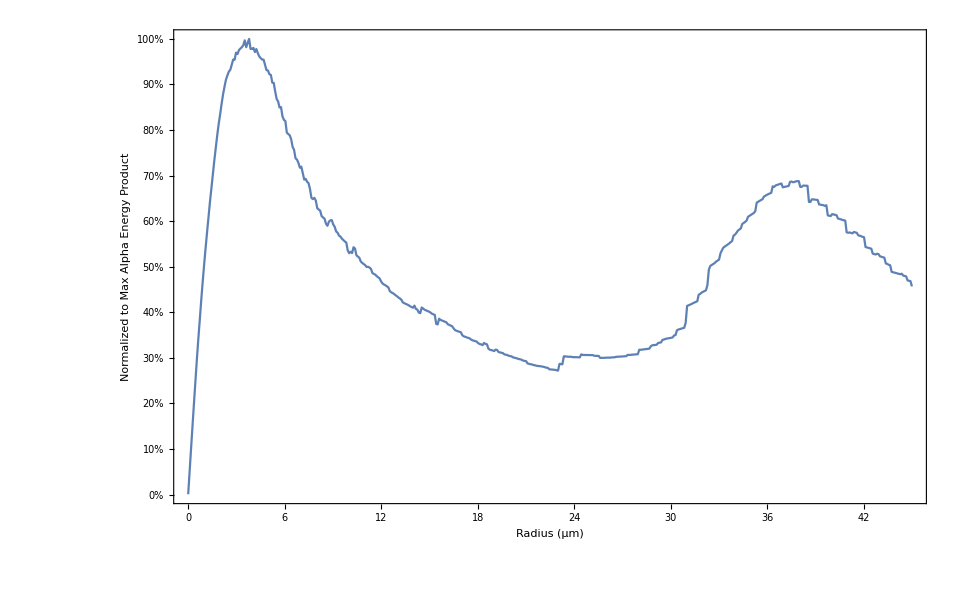

```mathematica
data=Transpose@{radii,TIon/Max[TIon]*100};
ListLinePlot[data,Frame-> True, FrameLabel-> {"Radius (µm)","Normalized to Max Alpha Energy Product"},PlotRange-> All,BaseStyle->{FontSize-> 28},FrameTicks->{{{{0.0,"0%"},{10,"10%"},{20,"20%"},{30,"30%"},{40,"40%"},{50,"50%"},{60,"60%"},{70,"70%"},{80,"80%"},{90,"90%"},{100,"100%"}},None},{Automatic,None}}]
```

```mathematica
findmax[r1_,r2_]:=radii[[Position[TIon,Max[TIon[[Position[radii,Nearest[radii,r1,1][[1]]][[1,1]];;Position[radii,Nearest[radii,r2,1][[1]]][[1,1]]]]]][[1,1]]]]
```

```mathematica
findmax[0,10]
```

3.78849

```mathematica
findmax[30,40]
```

37.9661